```mathematica
(* Everything in SI units *)
L = 1; (* Length of string *)
T = 65.0; (* Tension in string *)
μ = 0.005; (* Linear mass density *)
Y = 2.0*10^11; (* Young's modulus *)
r = 0.00135; (* Radius of string *)
A = π r^2;  (* Cross-sectional area *)
k = r/2;(* Radius of gyration *) 
β = (π^2 Y A k^2)/(T L^2);
v = Sqrt[T/μ];
ff0 = v/(2 L);
(* Plotting mode frequencies for fixed β *)
n = {1,2,3,4,5,6};
nfreq = {0.016894,0.007641,0.004455,0.002911,0.002030,0.001489};
afreq = Table[i ff0 Sqrt[1+ i^2 β], {i, 1, 6}];
af0 = Table[i ff0, {i, 1, 6}];
```

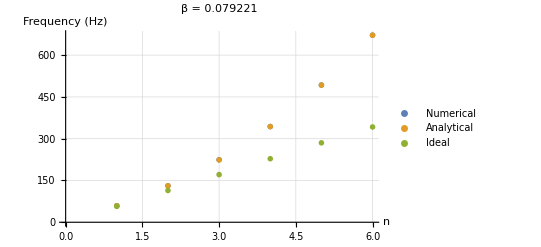

```mathematica
ListPlot[{1/Around[nfreq, 0.000005], afreq, af0}, PlotLegends->{"Numerical", "Analytical", "Ideal"}, PlotMarkers->"OpenMarkers", AxesLabel->{"n", "Frequency (Hz)"}, GridLines->Automatic, PlotLabel->"β = 0.079221"]
```

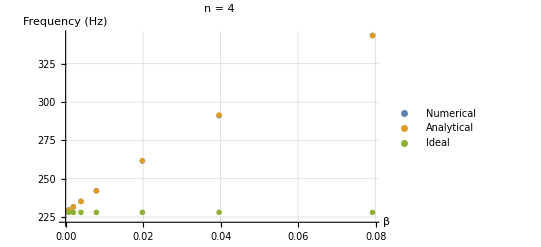

```mathematica
(* Plotting the n=4 mode frequency for different values of β *)
ndata = {0.004355,0.004318,0.004251,0.004130,0.003823,0.003435,0.002912};
adata = Table[4 ff0 Sqrt[1 + 4^2 * i *10^9*(π^2 A k^2)/(T L^2)], {i, {2, 5, 10, 20, 50, 100, 200}}];
idata = Table[4 ff0 , {i, {2, 5, 10, 20, 50, 100, 200}}];
yrange = Table[i *10^9*(π^2 A k^2)/(T L^2), {i, {2, 5, 10, 20, 50, 100, 200}}];
ListPlot[TemporalData[{1/Around[ndata, 0.000005], adata, idata}, {yrange}], PlotMarkers->"OpenMarkers", PlotLegends->{"Numerical", "Analytical", "Ideal"}, AxesLabel->{"β", "Frequency (Hz)"}, GridLines->Automatic, PlotLabel->"n = 4"]
```